```mathematica
x[egamma_,MBH_]:=egamma/(1.058(10^10/MBH));

(* parameterization in Eq. (31-34) of 1510/.04372 *)
Aparam=6.339 10^23;
Bparam=1.1367 10^24;
ThetaS[u_]:=0.5*(1.+Tanh[10.*u]);

d2NdEdtfrag[egamma_,MBH_]:=Aparam*x[egamma,MBH ]*(1-ThetaS[x[egamma,MBH ]-0.3])+Bparam*Exp[-x[egamma,MBH ]]*ThetaS[x[egamma,MBH ]-0.3]/(x[egamma,MBH ]*(x[egamma,MBH ]+1));

Ffunc[y_]:=If[y<2,1.,Exp[-0.0962-1.982(Log[y]-1.908)*(1.+Tanh[20.*(Log[y]-1.908)])]]


d2NdEdtdirect[egamma_,MBH_]:=(1.13 10^19 (x[egamma,MBH ])^6)/(Exp[x[egamma,MBH ]]-1.)*Ffunc[x[egamma,MBH ]]
```

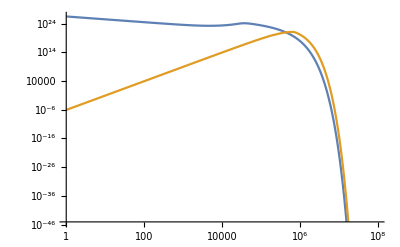

```mathematica
MBHl=10^5;
LogLogPlot[{d2NdEdtfrag[eg,MBHl],d2NdEdtdirect[eg,MBHl]},{eg,1,10^8}]

PhotonFlux[MBH_,Elow_,Ehigh_]:=NIntegrate[d2NdEdtfrag[egamma,MBH]+d2NdEdtdirect[egamma,MBH],{egamma,Elow,Ehigh}];
```

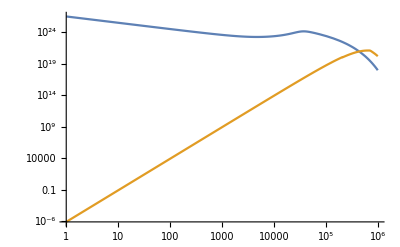

```mathematica
(* Plot[{PhotonFlux[MBH,30 10^3 ,100  ]},{MBH,10^-3,10^13}]*)
```

NIntegrate::inumr: The integrand (8.056834400594043`*^-42\ SuperscriptBox[egamma, 6]\ SuperscriptBox[MBH, 6]\ If[9.45179584120983`*^-11\ egamma\ MBH < 2, 1.`, Exp[-0.0962` - 1.982`\ Plus[«2»]\ Plus[«2»]]])/(-1.` + SuperscriptBox[ⅇ, 9.45179584120983`*^-11\ egamma\ MBH]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{30000, 100}}.

NIntegrate::inumr: The integrand (8.05683×10^-42 egamma^6 MBH^6 If[9.4518×10^-11 egamma MBH<2,1.,Exp[-0.0962-1.982 Plus[«2»] Plus[«2»]]])/(-1.+ⅇ^(9.4518×10^-11 egamma MBH))+(6.01314×10^33 ⅇ^(«1») (1.+Tanh[10. («1»)]))/(egamma MBH (1+9.4518×10^-11 «6» MBH))+5.99149×10^13 egamma MBH (1-0.5 (1.+Tanh[10. Plus[«2»]])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{30000.,100.}}.

NIntegrate::inumr: The integrand (8.05683×10^-42 egamma^6 MBH^6 If[9.4518×10^-11 egamma MBH<2,1.,Exp[-0.0962-1.982 Plus[«2»] Plus[«2»]]])/(-1.+ⅇ^(9.4518×10^-11 egamma MBH))+(6.01314×10^33 ⅇ^(«1») (1.+Tanh[10. («1»)]))/(egamma MBH (1+9.4518×10^-11 «6» MBH))+5.99149×10^13 egamma MBH (1-0.5 (1.+Tanh[10. Plus[«2»]])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{30000,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
(*LogLogPlot[PhotonFlux[MPBH,100 10^-6,300 10^-6]/PhotonFlux[MPBH,50 10^-6,100 10^-6],{MPBH,10^3,10^13},Frame->True,FrameLabel->{"BH mass [kg]","Flux[100-300 keV] over Flux[50-100 keV]"},LabelStyle->Directive[Bold],AspectRatio->1]*)
```

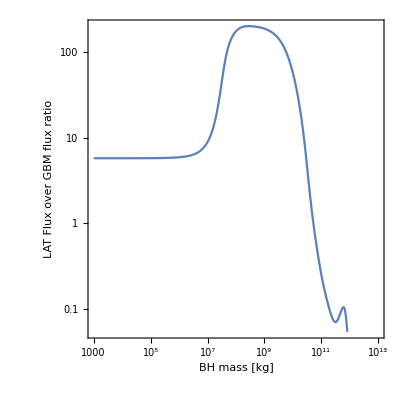

```mathematica
(* This is the LAT to GBM hardness ratio*)
LogLogPlot[PhotonFlux[MPBH,100 10^-3,100]/PhotonFlux[MPBH,30 10^-3,100 10^-3],{MPBH,10^3,10^13},Frame->True,FrameLabel->{ "BH mass [kg]","LAT Flux over GBM flux ratio"},LabelStyle->Directive[Bold],AspectRatio->1]
```

```mathematica
MPBH=10^6;
PhotonFlux[MPBH,100 10^-6,300 10^-6]/PhotonFlux[MPBH,50 10^-6,100 10^-6]

MPBH=10^6;
PhotonFlux[MPBH,100 10^-3,100]/PhotonFlux[MPBH,30 10^-3,100 10^-3]
```

1.58496

5.89222